# Chemoids Implemented as Hypergraph Rewriting

```mathematica
PacletUninstall["WolframInstitute/Hypergraph"]
PacletInstall["https://wolfr.am/Hypergraph.paclet"]
<<WolframInstitute`Hypergraph`
```

PacletObject[…]

```mathematica
HyperCool[hyp_]:=Hypergraph[hyp,VertexStyle->White,EdgeStyle->White,Background->Black,VertexLabelStyle->White]
```

```mathematica
HyperCool3D[hyp_]:=Hypergraph3D[hyp,VertexStyle->White,EdgeStyle->White,Background->Black,VertexLabelStyle->White]
```

## Category

### Semicategory

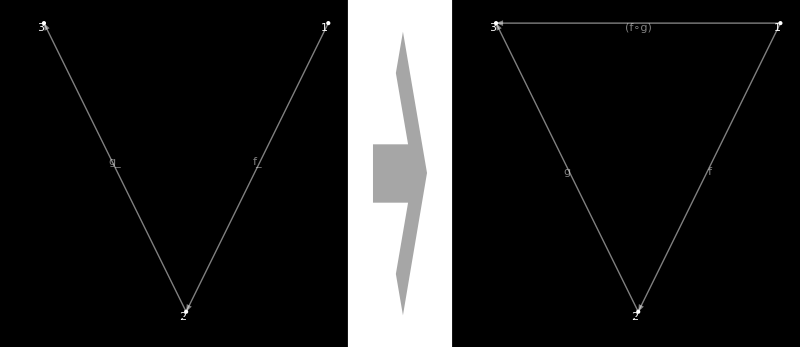

```mathematica
CatCompInput=HyperCool@Hypergraph[{1,2,3},Hyperedges[{1,2}->f_,{2,3}->g_],"EdgeSymmetry"->"Ordered",EdgeLabels->Placed["EdgeTag",Bottom],VertexLabels->{1->A_,2->B_,3->C_}];
CatCompOutput=HyperCool@Hypergraph[{1,2,3},Hyperedges[{1,2}->f,{2,3}->g,{1,3}->Row[{"(",f∘g,")"}]],"EdgeSymmetry"->"Ordered",EdgeLabels->Placed["EdgeTag",Top],VertexLabels->{1->A,2->B,3->C},VertexCoordinates->Thread[VertexList[CatCompInput]->HypergraphEmbedding[CatCompInput]]];
CatComp=HypergraphRule[CatCompInput,CatCompOutput]
```

Associativity:

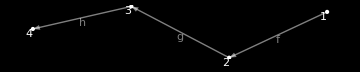

```mathematica
AssocGraph=HyperCool@Hypergraph[{{1,2}->"f",{2,3}->"g",{3,4}->"h"},"EdgeSymmetry"->"Ordered",EdgeLabels->Placed["EdgeTag",Top],VertexLabels->{1->X,2->Y,3->Z,4->W}]
```

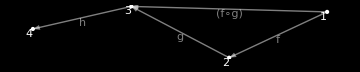
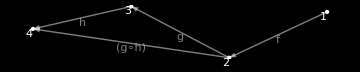
{<|Hypergraph→-Graphics-,MatchVertices→{1,2,3},MatchEdges→{{1,2},{2,3}},MatchEdgePositions→{{1},{2}},NewVertices→{},NewEdges→{{1,2}→f,{2,3}→g,{1,3}→(f∘g)},DeletedVertices→{},RuleVertexMap→{1→1,2→2,3→3}|>,<|Hypergraph→-Graphics-,MatchVertices→{2,3,4},MatchEdges→{{2,3},{3,4}},MatchEdgePositions→{{2},{3}},NewVertices→{},NewEdges→{{2,3}→g,{3,4}→h,{2,4}→(g∘h)},DeletedVertices→{},RuleVertexMap→{1→2,2→3,3→4}|>}

```mathematica
CatComp@AssocGraph
```

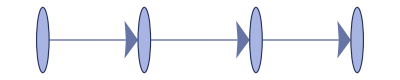
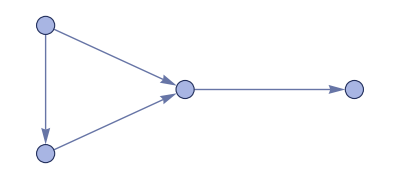
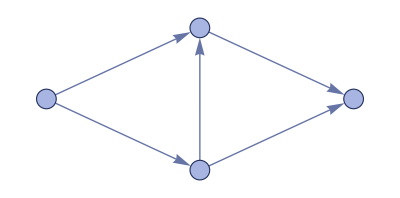
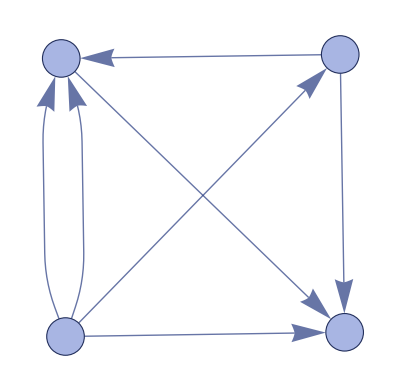
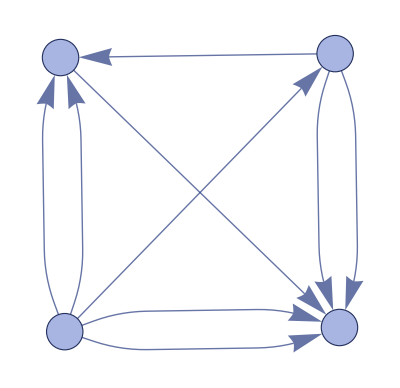

```mathematica
ResourceFunction["WolframModel"][{{x,y},{y,z}}->{{x,y},{y,z},{x,z}},{{X,Y},{Y,Z},{Z,W}},4,"StatesPlotsList"]
```

```mathematica
NestGraph[h|->CatComp[h][[All,"Hypergraph"]],{AssocGraph},3,
VertexShapeFunction->Function[Inset[Framed[SimpleHypergraphPlot[#2,ImageSize->150,AspectRatio->1/2],FrameStyle->Black],#1,#3]],PerformanceGoal->"Quality"]
```

-Graphics-

Finds that ( f o ( g o h ) ) = ( ( f o g ) o h ).

### Unar

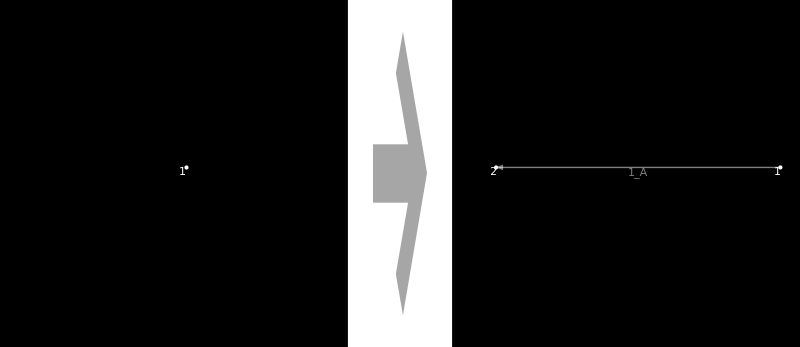

```mathematica
UnarInput=HyperCool@Hypergraph[{1},Hyperedges[],"EdgeSymmetry"->"Ordered",VertexLabels->{1->A_},EdgeLabels->Placed["EdgeTag",Bottom]];
UnarOutput=HyperCool@Hypergraph[{1,2},Hyperedges[{1,2}->Subscript["1", A]],"EdgeSymmetry"->"Ordered",VertexLabels->{1->A,2->A},EdgeLabels->Placed["EdgeTag",Top]];
Unit=HypergraphRule[UnarInput,UnarOutput]
```

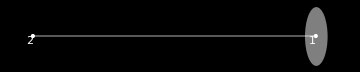

```mathematica
TestUnit=HyperCool@Hypergraph[{1,2},{{1},{1,2}}, VertexLabels->{1->X,2->Y}]
```

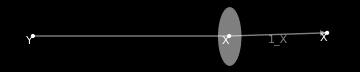
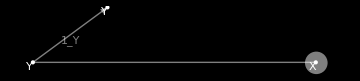
{<|Hypergraph→-Graphics-,MatchVertices→{1},MatchEdges→{},MatchEdgePositions→{},NewVertices→{v7934},NewEdges→{{1,v7934}→1_X},DeletedVertices→{},RuleVertexMap→{1→1,2→v7934}|>,<|Hypergraph→-Graphics-,MatchVertices→{2},MatchEdges→{},MatchEdgePositions→{},NewVertices→{v7934},NewEdges→{{2,v7934}→1_Y},DeletedVertices→{},RuleVertexMap→{1→2,2→v7934}|>}

```mathematica
Unit@TestUnit
```

### Category

## Dagger

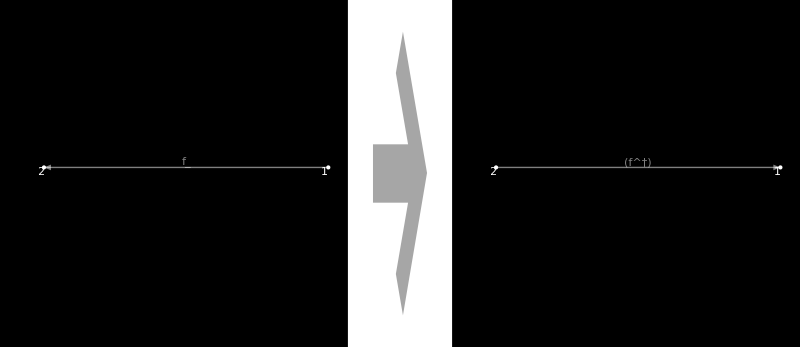

```mathematica
DaggerInput=HyperCool@Hypergraph[{1,2},Hyperedges[{1,2}->f_],"EdgeSymmetry"->"Ordered",EdgeLabels->Placed["EdgeTag",Bottom],VertexLabels->{1->A_,2->B_}];
DaggerOutput=HyperCool@Hypergraph[{1,2},Hyperedges[{2,1}->Row[{"(",SuperDagger[f],")"}]],"EdgeSymmetry"->"Ordered",EdgeLabels->Placed["EdgeTag",Bottom],VertexLabels->{1->A,2->B},VertexCoordinates->Thread[VertexList[DaggerInput]->HypergraphEmbedding[DaggerInput]]];
Dagger=HypergraphRule[DaggerInput,DaggerOutput]
```

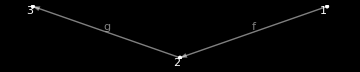

```mathematica
DaggerV=HyperCool@Hypergraph[{1,2,3},{{1,2}->f,{2,3}->g},VertexLabels->{1->A,2->B,3->C},"EdgeSymmetry"->"Ordered",EdgeLabels->Placed["EdgeTag",Bottom]]
```

```mathematica
NestGraph[h|->Join[CatComp[h][[All,"Hypergraph"]],Dagger[h][[All,"Hypergraph"]]],{DaggerV},3,VertexShapeFunction->Function[Inset[Framed[SimpleHypergraphPlot[#2,ImageSize->150,AspectRatio->1/2],FrameStyle->Black],#1,#3]],PerformanceGoal->"Quality"]
```

-Graphics-

## Heapoid

### Semiheapoid

#### ZigZag Composition

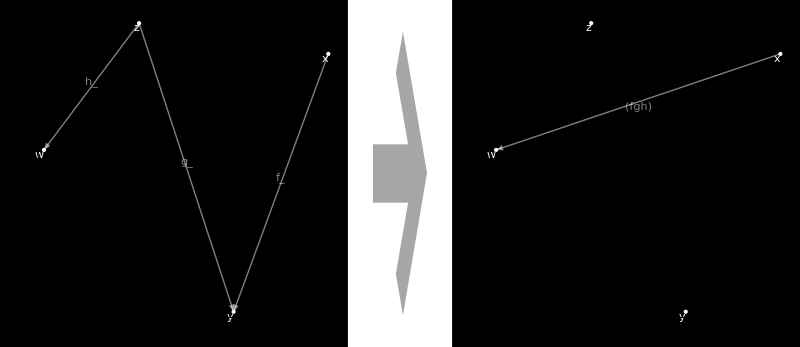

```mathematica
ZigZagCompInput=HyperCool@Hypergraph[{x,y,z,w},Hyperedges[{x,y}->f_,{z,y}->g_,{z,w}->h_],"EdgeSymmetry"->"Ordered",EdgeLabels->Placed["EdgeTag",Bottom],VertexLabels->Automatic];
ZigZagCompOutput=HyperCool@Hypergraph[{x,y,z,w},Hyperedges[{x,w}->Row[{"(",f,g,h,")"}]],"EdgeSymmetry"->"Ordered",EdgeLabels->Placed["EdgeTag",Top],VertexCoordinates->Thread[VertexList[ZigZagCompInput]->HypergraphEmbedding[ZigZagCompInput]],VertexLabels->Automatic];
ZigZagComp=HypergraphRule[ZigZagCompInput,ZigZagCompOutput]
```

Semiheap Associativity:

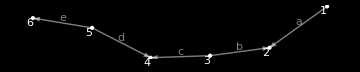

```mathematica
SemiheapZigZagHyp=Hypergraph[HyperCool@Hypergraph[{{1,2}->a,{3,2}->b,{3,4}->c,{5,4}->d,{5,6}->e},"EdgeSymmetry"->"Ordered",EdgeLabels->"EdgeTag"],EdgeLabels->Placed["EdgeTag",Bottom],VertexLabels->Automatic]
```

```mathematica
NestGraph[h|->ZigZagComp[h][[All,"Hypergraph"]],{SemiheapZigZagHyp},2,VertexShapeFunction->Function[Inset[Framed[SimpleHypergraphPlot[#2,ImageSize->150,AspectRatio->1/2],FrameStyle->Black],#1,#3]],PerformanceGoal->"Quality"]
```

-Graphics-

#### Fish Composition

```mathematica
FishCompInput=HyperCool@Hypergraph[{x,y,p,q,r,z},Hyperedges[{y,x,p}->f_,{q,p,r}->g_,{q,r,z}->h_],"EdgeSymmetry"->"Unordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic];
FishCompOutput=HyperCool@Hypergraph[{x,y,p,q,r,z},Hyperedges[{y,x,z}->Row[{"(",f, g,h,")"}]],"EdgeSymmetry"->"Unordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic];
FishComp=HypergraphRule[FishCompInput,FishCompOutput]
```

```mathematica
VertexCoordinates->Thread[VertexList[FishCompInput]->HypergraphEmbedding[FishCompInput]]
```

Semiheap Associativity:

```mathematica
SemiheapFishHyp=HyperCool@Hypergraph[{{1,2,3}->a,{4,3,5}->b,{4,5,6}->c,{7,6,8}->d,{7,8,9}->e},"EdgeSymmetry"->"Unordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic]
```

-Graphics-

```mathematica
NestGraph[h|->FishComp[h][[All,"Hypergraph"]],{SemiheapFishHyp},2,VertexShapeFunction->Function[Inset[Framed[SimpleHypergraphPlot[#2,ImageSize->150,AspectRatio->1/2],FrameStyle->Black],#1,#3]],PerformanceGoal->"Quality"]
```

-Graphics-

Finds that ( a b ( c d e ) ) = ( a ( d c b ) e ) = ( a b ( c d e ) ).

### Malcevoid

#### ZigZag Left Biunit

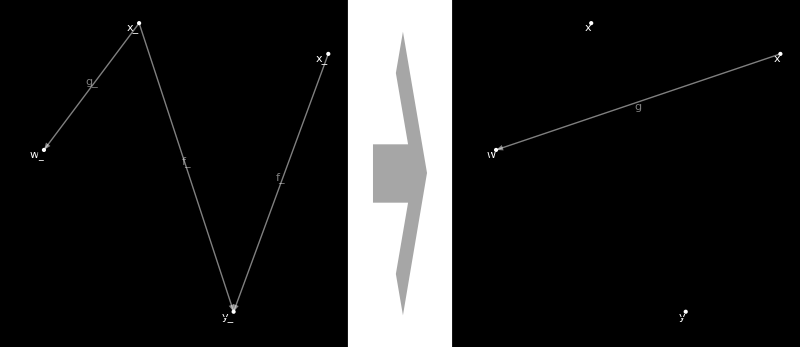

```mathematica
ZigZagLBiunitInput=HyperCool@Hypergraph[{1,2,3,4},Hyperedges[{1,2}->f_,{3,2}->f_,{3,4}->g_],"EdgeSymmetry"->"Ordered",EdgeLabels->Placed["EdgeTag",Bottom],VertexLabels->{1->x_,2->y_,3->x_,4->w_}];
ZigZagLBiunitOutput=HyperCool@Hypergraph[{1,2,3,4},Hyperedges[{1,4}->g],"EdgeSymmetry"->"Ordered",EdgeLabels->Placed["EdgeTag",Top],VertexLabels->{1->x,2->y,3->x,4->w},VertexCoordinates->Thread[VertexList[ZigZagLBiunitInput]->HypergraphEmbedding[ZigZagLBiunitInput]]];
ZigZagLBiunit=HypergraphRule[ZigZagLBiunitInput,ZigZagLBiunitOutput]
```

### Heapoid

## Operad

```mathematica
Ope1Input=HyperCool@Hypergraph[{1,2,3,4},Hyperedges[{1,2}->f_,{2,3,4}->g_],"EdgeSymmetry"->"Ordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic];
Ope1Output=HyperCool@Hypergraph[{1,2,3,4},Hyperedges[{1,3,4}->Row[{"(",f∘g,")"}]],"EdgeSymmetry"->"Ordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic,VertexCoordinates->Thread[VertexList[Ope1Input]->HypergraphEmbedding[Ope1Input]]];
Ope1Comp=HypergraphRule[Ope1Input,Ope1Output]
```

-Graphics-

```mathematica
Ope11Input=HyperCool@Hypergraph[{1,2,3,4,5},Hyperedges[{1,2}->f_,{2,3,4,5}->g_],"EdgeSymmetry"->"Ordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic];
Ope11Output=HyperCool@Hypergraph[{1,2,3,4,5},Hyperedges[{1,3,4,5}->Row[{"(",f∘g,")"}]],"EdgeSymmetry"->"Ordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic,VertexCoordinates->Thread[VertexList[Ope1Input]->HypergraphEmbedding[Ope1Input]]];
Ope11Comp=HypergraphRule[Ope11Input,Ope11Output]
```

-Graphics-

```mathematica
Ope2Input=HyperCool@Hypergraph[{1,2,3,4,5},Hyperedges[{1,2,3}->f_,{3,4,5}->g_],"EdgeSymmetry"->"Ordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic];
Ope2Output=HyperCool@Hypergraph[{1,2,3,4},Hyperedges[{1,2,4,5}->Row[{"(",f∘g,")"}]],"EdgeSymmetry"->"Ordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic,VertexCoordinates->Thread[VertexList[Ope1Input]->HypergraphEmbedding[Ope1Input]]];
Ope2Comp=HypergraphRule[Ope2Input,Ope2Output]
```

-Graphics-

```mathematica
OpeAssocTest=HyperCool@Hypergraph[{0,1,2,3,4,5},Hyperedges[{0,1}->f,{1,2,3}->g,{3,4,5}->h],"EdgeSymmetry"->"Ordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic]
```

-Graphics-

```mathematica
NestGraph[h|->Join[Ope1Comp[h][[All,"Hypergraph"]],Ope11Comp[h][[All,"Hypergraph"]],Ope2Comp[h][[All,"Hypergraph"]]],{OpeAssocTest},3,VertexShapeFunction->Function[Inset[Framed[SimpleHypergraphPlot[#2,ImageSize->150,AspectRatio->1/2],FrameStyle->Black],#1,#3]],PerformanceGoal->"Quality"]
```

-Graphics-

## Tetroid

```mathematica
BMInput=HyperCool@Hypergraph[{{1, 2, 4}->r_, {2, 3, 4}->g_,{3, 1, 4}->b_},"EdgeSymmetry"->"Unordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic];
BMOutput=HyperCool@Hypergraph[{{1, 2, 3}->Row[{"(",r, g,b,")"}]},"EdgeSymmetry"->"Unordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic];
BMRule=HypergraphRule[BMInput,BMOutput]
```

-Graphics-

```mathematica
BMState=HyperCool@Hypergraph[{1, 2, 3, 4, 5, 6, 7}, Hyperedges[{1, 2, 5}->a, {2, 4, 5}->b,{4, 1, 5}->c, {2, 3, 7}->d, {3, 4, 7}->e, {4, 2, 7}->f, {3, 1, 6}->g, 
   {6, 4, 3}->h, {1, 4, 6}->i],"EdgeSymmetry"->"Unordered",EdgeLabels->"EdgeTag",VertexLabels->Automatic]
```

-Graphics-

```mathematica
NestGraph[h|->BMRule[h][[All,"Hypergraph"]],{BMState},4,VertexShapeFunction->Function[Inset[Framed[SimpleHypergraphPlot[#2,ImageSize->150,AspectRatio->1/2],FrameStyle->Black],#1,#3]],PerformanceGoal->"Quality"]
```

-Graphics-

Models the sequential evaluation tree of ((a,b,c),(d,e,f),(g,h,i)).